# SmoothStep

A sigmoidal interpolation function.

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
SmoothStep[x_]:=Piecewise[{{0, x<0}, {1, x>1}, {3 x^2-2 x^3, True}}]
```

```mathematica
SmoothStep[x_,{min_,max_}]:=SmoothStep[Rescale[x,{min,max}]]
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

SmoothStep[x]

returns a sigmoidal, Hermite interpolation between [0,1] for x on [0,1].

SmoothStep[x,{min,max}]

returns a sigmoidal, Hermite interpolation between [0,1] for x on [min,max].

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

SmoothStep is an interpolation function commonly used in computer graphics.

The SmoothStep implementation is consistent with the GL and RenderMan (RSL) shading languages.

SmoothStep[x] clamps to 0 or 1 for x less than or greater than 0 or 1, respectively.

SmoothStep[x, {min,max}] is the same as the RenderMan smoothstep(min,max,x) invocation.

The original SmoothStep is not 2nd order continuous at either x=0 or x=1. This creates discontinuities. SmootherStep solves this problem.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

The function is sigmoidal. Inputs < 0.5 underestimate the input:

```mathematica
SmoothStep[0.1]
```

0.028

Values > 0.5 do the opposite:

```mathematica
SmoothStep[0.7]
```

0.784

The function:

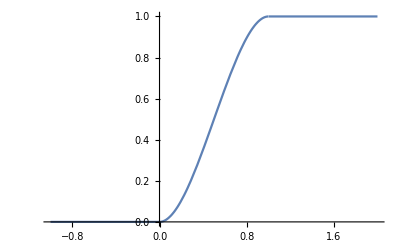

```mathematica
Plot[SmoothStep[x],{x,-1,2}]
```

### Scope

The standard form:

```mathematica
SmoothStep[0.5]
```

0.5

Optionally, one can specify an input domain:

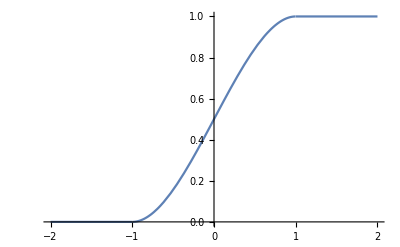

```mathematica
Plot[SmoothStep[x,{-1,1}],{x,-2,2}]
```

### Applications

Smoothly interpolate with more gradual changes at the start and stop of the interpolation domain:

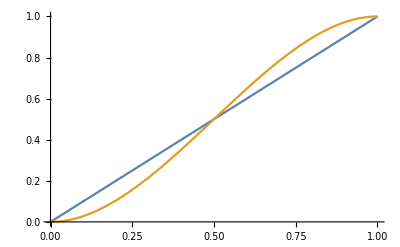

```mathematica
Plot[{x,SmoothStep[x]},{x,0,1}]
```

Interpolate colors:

```mathematica
Table[Hue[x],{x,0,1,.1}]
```

{Hue[0.],Hue[0.1],Hue[0.2],Hue[0.30000000000000004],Hue[0.4],Hue[0.5],Hue[0.6000000000000001],Hue[0.7000000000000001],Hue[0.8],Hue[0.9],Hue[1.]}

```mathematica
Table[Hue[SmoothStep[x]],{x,0,1,.1}]
```

{Hue[0.],Hue[0.028000000000000004],Hue[0.10400000000000002],Hue[0.21600000000000005],Hue[0.3520000000000001],Hue[0.5],Hue[0.6480000000000001],Hue[0.784],Hue[0.8960000000000001],Hue[0.972],Hue[1.]}

### Possible Issues

SmoothStep is 2nd order discontinuous at x=0 and x=1:

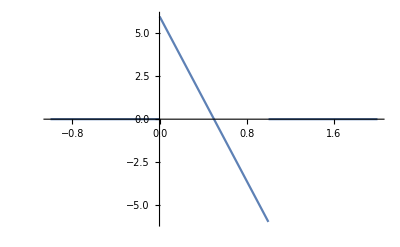

```mathematica
Plot[SmoothStep''[x],{x,-1,2}]
```

### Neat Examples

SmoothStep approximates the animation technique of ‘ease-in / ease-out’:

```mathematica
Animate[Graphics[Text["Zoom!",{SmoothStep[x],0}],PlotRange->{{-.1,1.1},{-.1,.1}}],{x,-1,2}]
```

-Graphics-

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Flip Phillips

flipphillips.com

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

interpolation

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

UnitStep

Rescale

HeavisideTheta

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Perlin, K. 1985. An Image Synthesizer. In Computer Graphics (Proceedings of ACM SIGGRAPH 85), 24. 3.

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

Wikipedia on smoothstep: https://en.wikipedia.org/wiki/Smoothstep

Perlin et al.’s Texturing & Modeling: https://books.google.com/books?id=F4t-5zSsqr4C

RenderMan smoothstep documentation: https://renderman.pixar.com/resources/RenderMan_20/rslFunctions.html#step

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
SmoothStep/@{0,.5,1} == {0,.5,1}
```

True

## Author Notes

NA

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

The second form is included since may computer graphics routines use that form. Also, see the companion submission ‘SmootherStep’.
I tried three different ways of putting links into the references, yet, failures each time. A documented example might be nice in future versions of the template.
My ‘url’ self promotion in the ‘submitter’ box fails the checker with a ‘no author information’ error?

ResourceObject::notfname: The ResourceObject SmootherStep could not be found.

I couldn’t include the companion function because I haven’t submitted / hasn’t been accepted yet. Should I wait then add and ‘update’ the entry?